```mathematica
(* Sets the Base directory, changing which files are easiest to acces. *)
dropBoxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns","18-03-06_RubidiumOnWalls"}];
If[SystemInformation["Kernel","MachineName"]=="poke",
folder=FileNameJoin[{"/","home","karl",dropBoxOn}]; ,(* Home coputer is Linux, so needs "/" at beginning *)
folder=FileNameJoin[{"C:","Users","kahrendsen2",dropBoxOn}];(* Lab computer is Windows, so needs "C:" at beginning"*)];

(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{folder}]
SetDirectory[dataFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",1],DirectoryQ];
For[i=Length[directories],i>0,i--,
Print[i -> directories[[i]]];]
(* set rootFolder to the folder name containing the desired Files *)
rootFolder=FileNameJoin[{dataFolder}];
SetDirectory[rootFolder];
(* Obtain the filenames of the rotation data and print them out.*)
scanFiles=FileNames["FDayScan"~~RegularExpression[".{25,25}"]~~"Analysis.dat"];
rotationFiles=FileNames["FDayRotation"~~RegularExpression[".{25,25}"]~~"Analysis.dat"];
```

C:\Users\kahrendsen2\Dropbox\00School\research\DataRuns\18-03-06_RubidiumOnWalls

1→analysis

## Inputting data from Timestamps

```mathematica
(*Input the timestamps of the no pump files in the following array*)
autoRunHeatingTape={"234617","005201","020801","033002","045202","061201","073402","085602"}
resOffHeatOn={"113500"}
resOnHeatOn={"152157"}
resOnHeatOffMagnetsOff={"192628"}
resOnHeatOff={"205304"}
resCooling={"223457","065845","082136"}



fileTimestamp=Join[autoRunHeatingTape,resOffHeatOn,resOnHeatOn,resOnHeatOffMagnetsOff,resOnHeatOff,resCooling]
(* Record the baseline angle, the angle of the probe polarization when the magnets are off and the pump laser is off *)
baselineAngle=.134456;

(* Iterates through each of the timestamps above and calculates the number density from the Faraday Rotation data. *)
pdata={};
ndata={};
For[i=1,i≤Length[fileTimestamp],i++,
ndataLine=ProcessFaradayScanFile[scanFiles,fileTimestamp[[i]],baselineAngle];
AppendTo[ndata,ndataLine];
pdataLine=ProcessRbPolarizationFileSequence[scanFiles,fileTimestamp[[i]],baselineAngle,3];
AppendTo[pdata,pdataLine];

];

nstuff=Dataset[ndata];
pstuff=Dataset[pdata];
```

{234617,005201,020801,033002,045202,061201,073402,085602}

{113500}

{152157}

{192628}

{205304}

{223457,065845,082136}

{234617,005201,020801,033002,045202,061201,073402,085602,113500,152157,192628,205304,223457,065845,082136}

General::prng: Value of option PlotRange -> {-0.01+Min[{{11.0776,0.15574},{11.0302,0.160222},{10.5558,0.154129},{10.0339,0.14934},{9.51212,0.153538},{8.94286,0.162094},{8.3736,0.171792},{7.80434,0.180191},{7.18764,0.209068},«5»,{-8.98801,0.163638},{-9.69952,0.163554},{-10.411,0.16015},{-11.17,0.156252},{-11.8815,0.153199},{-12.593,0.148709},{-13.3519,0.163358},{-14.1582,0.159337}}[Max,2],«1»],0.01+«1»} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::prng: Value of option PlotRange -> {-0.01+Min[{{11.0776,0.15574},{11.0302,0.160222},{10.5558,0.154129},{10.0339,0.14934},{9.51212,0.153538},{8.94286,0.162094},{8.3736,0.171792},{7.80434,0.180191},{7.18764,0.209068},«5»,{-8.98801,0.163638},{-9.69952,0.163554},{-10.411,0.16015},{-11.17,0.156252},{-11.8815,0.153199},{-12.593,0.148709},{-13.3519,0.163358},{-14.1582,0.159337}}[Max,2],«1»],0.01+«1»} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {-0.01+Min[{{11.0776,0.15574},{11.0302,0.160222},{10.5558,0.154129},{10.0339,0.14934},{9.51212,0.153538},{8.94286,0.162094},{8.3736,0.171792},{7.80434,0.180191},{7.18764,0.209068},«5»,{-8.98801,0.163638},{-9.69952,0.163554},{-10.411,0.16015},{-11.17,0.156252},{-11.8815,0.153199},{-12.593,0.148709},{-13.3519,0.163358},{-14.1582,0.159337}}[Max,2],«1»],0.01+«1»} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of General::prng will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {0.080006,0.142144,0.159729,0.173214,0.172132,0.167212,0.182893,0.175698,0.177709,0.194329,0.207676,0.243471,0.367495,0.0343641,0.12488,0.288555,0.225339,0.359309,0.0649244,«13»,0.173558,0.153279,0.150278,0.147083,0.140715,0.135568,0.146974,0.136637,0.136565,0.140502,0.143316,0.142303,0.134341,0.141245,0.143793,0.144414,0.135645,0.132618}+{«1»} cannot be combined.

Transpose::nmtx: The first two levels of {{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,0.19978,0.220695,0.249418,«14»,-0.238258,-0.211913,-0.190814,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},{«1»}+{«1»}} cannot be transposed.

Thread::tdlen: Objects of unequal length in {0.171382,0.161092,0.161741,0.149471,0.161054,0.165301,0.171174,0.170971,0.169053,0.179094,0.200644,0.218513,0.31142,0.119202,0.0682197,0.272773,0.214622,0.316244,0.171295,«12»,0.192068,0.158509,0.161421,0.146709,0.141209,0.144155,0.160008,0.140136,0.141007,0.138485,0.135252,0.152098,0.144456,0.139949,0.140896,0.147316,0.151276,0.13708,0.151371}+«1» cannot be combined.

Transpose::nmtx: The first two levels of {{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,0.19978,0.220695,0.249418,«14»,-0.238258,-0.211913,-0.190814,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},{«1»}+{«1»}} cannot be transposed.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Part::partw: Part 2 of «1» does not exist.

Thread::tdlen: Objects of unequal length in {-0.153189,-0.155567,-0.166112,-0.174197,-0.188498,-0.187067,-0.198256,-0.207272,-0.240414,-0.352707,-0.225841,-0.120126,-0.340102,-0.350545,-0.373201,-0.0887104,-0.323432,-0.403371,«4»,0.855476,-0.530569,-0.24277,-0.184006,-0.174913,-0.154977,-0.147675,-0.141078,-0.152315,-0.146396,-0.136469,-0.1438,-0.130844,-0.135856,-0.134553,-0.147543,-0.143944,-0.140698}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,0.19978,0.220695,0.249418,«14»,-0.238258,-0.211913,-0.190814,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},{«1»}+{«1»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 2 of «1» does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: Transpose[«1»] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Transpose[{{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,0.19978,0.220695,«16»,-0.211913,-0.190814,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},{-«19»,«38»,-«19»}+«1»}]],},«5»].

ListPlot::lpn: Transpose[«1»] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Transpose[{{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,0.19978,0.220695,«16»,-0.211913,-0.190814,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},{-«19»,«38»,-«19»}+«1»}]],},«5»].

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partw: Part 2 of «1» does not exist.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partw: Part 2 of «1» does not exist.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Part::partw: Part 2 of «1» does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Transpose[{{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,0.19978,0.220695,«16»,-0.211913,-0.190814,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},{-«19»,«38»,-«19»}+«1»}]],},«5»].

Thread::tdlen: Objects of unequal length in {0.080006, 0.142144, 0.159729, 0.173214, 0.172132, 0.167212, 0.182893, 0.175698, 0.177709, 0.194329, 0.207676, 0.243471, 0.367495, 0.0343641, 0.12488, 0.288555, «18», 0.150278, 0.147083, 0.140715, 0.135568, 0.146974, 0.136637, 0.136565, 0.140502, 0.143316, 0.142303, 0.134341, 0.141245, 0.143793, 0.144414, 0.135645, 0.132618} + {«1»} cannot be combined.

Transpose::nmtx: The first two levels of {{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,0.19978,«19»,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},{«1»}+{«1»}} cannot be transposed.

Thread::tdlen: Objects of unequal length in {0.171382,0.161092,0.161741,0.149471,0.161054,0.165301,0.171174,0.170971,0.169053,0.179094,0.200644,0.218513,0.31142,0.119202,0.0682197,0.272773,«18»,0.146709,0.141209,0.144155,0.160008,0.140136,0.141007,0.138485,0.135252,0.152098,0.144456,0.139949,0.140896,0.147316,0.151276,0.13708,0.151371}+{-«19»,«38»,-«19»} cannot be combined.

Transpose::nmtx: The first two levels of {{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,0.19978,«19»,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},{«1»}+{«1»}} cannot be transposed.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Part::partw: Part 2 of LinearModelFit[Transpose[«1»],x$234106,x$234106][BestFitParameters] does not exist.

Thread::tdlen: Objects of unequal length in {-0.153189,-0.155567,-0.166112,-0.174197,-0.188498,-0.187067,-0.198256,-0.207272,-0.240414,-0.352707,-0.225841,-0.120126,-0.340102,-0.350545,-0.373201,-0.0887104,«9»,-0.184006,-0.174913,-0.154977,-0.147675,-0.141078,-0.152315,-0.146396,-0.136469,-0.1438,-0.130844,-0.135856,-0.134553,-0.147543,-0.143944,-0.140698}+{«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,0.19978,«19»,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},{«1»}+{«1»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Part::partw: Part 2 of LinearModelFit[Transpose[«1»],x$234106,x$234106][BestFitParameters] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: Transpose[{{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,0.19978,«19»,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},«1»+«1»}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Transpose[{{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,«20»,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},«1»}]],},«5»].

ListPlot::lpn: Transpose[{{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,0.19978,«19»,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},«1»+«1»}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Transpose[{{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,«20»,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},«1»}]],},«5»].

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partw: Part 2 of LinearModelFit[Transpose[«1»],x$234106,x$234106][BestFitParameters] does not exist.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

Part::partw: Part 2 of LinearModelFit[Transpose[«1»],x$234106,x$234106][BestFitParameters] does not exist.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Part::partw: Part 2 of LinearModelFit[Transpose[«1»],x$234106,x$234106][ParameterErrors] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[Transpose[{{0.0891272,0.0876449,0.0906605,0.0943111,0.097812,0.102571,0.107818,0.11302,0.119423,0.126595,0.134683,0.1429,0.153292,0.165313,0.180919,«20»,-0.17212,-0.156761,-0.142943,-0.132188,-0.122938,-0.114898,-0.106752,-0.100637,-0.0947569,-0.0895259,-0.0848422,-0.0806242,-0.0768058,-0.0733327,-0.0701602},«1»}]],},«5»].

```mathematica
pstuff[SortBy["time"]](*[Select[120>#["CurrTemp(Res)"]≥114&]]*)
nstuff[SortBy["time"]]
```

Dataset[<>]

Dataset[<>]

```mathematica
nstuff[All,{"Comments","n_rb","plot"}]
```

Dataset[<>]

```mathematica
Export["nrbVsTres.tsv",nstuff]
```

nrbVsTres.tsv

## Generating n_Rb Graphs

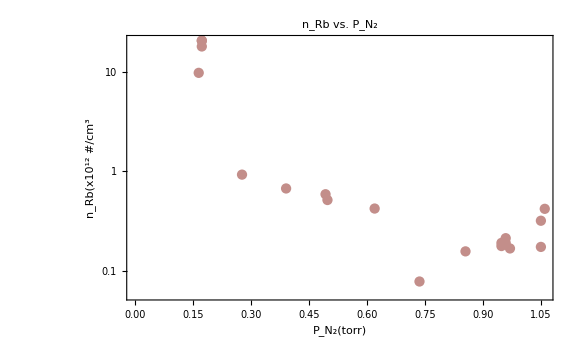

```mathematica
nVsTplotLabels={PlotLabel->"n_Rb vs. T_res",FrameLabel->{"T_res(°C)","n_Rb(x10^12 #/cm^3"}};
nVsBGPplotLabels={PlotLabel->"n_Rb vs. P_N_2",FrameLabel->{"P_N_2(torr)","n_Rb(x10^12 #/cm^3"}};

nvBGP=nstuff[All,{"CVGauge(N2)(Torr)","n_rb"}];
ListLogPlot[{nvBGP},nVsBGPplotLabels,PlotStyle->18,LabelStyle->20,Frame->True,GridLines->Automatic,ImageSize->Large]
```

## Generating P_Rb Graphs

Dataset[<>]

Dataset[<>]

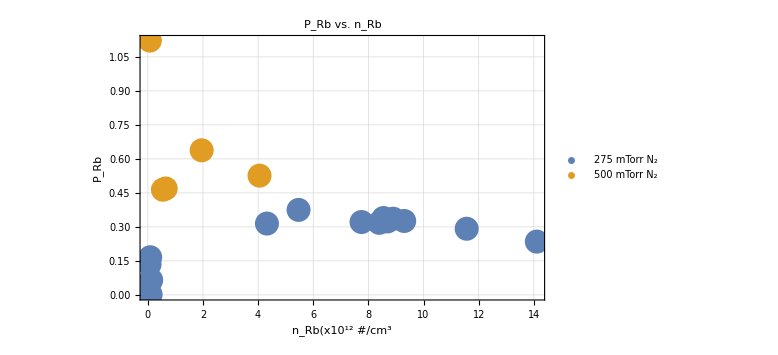

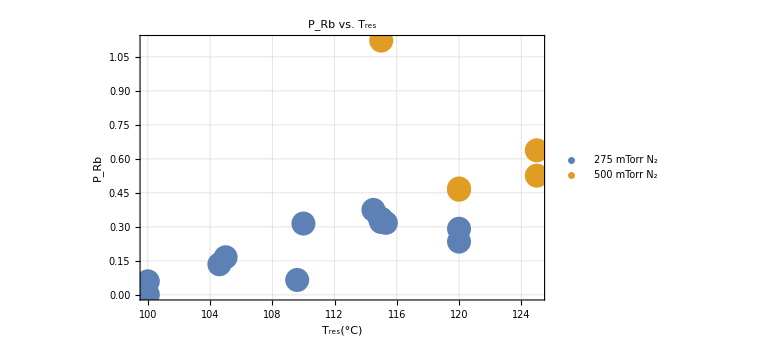

```mathematica
pVsTplotLabels={PlotLabel->"P_Rb vs. T_res",FrameLabel->{"T_res(°C)","P_Rb"}};
pVsnplotLabels={PlotLabel->"P_Rb vs. n_Rb",FrameLabel->{"n_Rb(x10^12 #/cm^3","P_Rb"}};

pVt275=pstuff[Select[#["CVGauge(N2)(Torr)"]<.3&]][All,{"CurrTemp(Res)","p_rb"}];
pVt500=pstuff[Select[#["CVGauge(N2)(Torr)"]≥.3&]][All,{"CurrTemp(Res)","p_rb"}]
pVn275=pstuff[Select[#["CVGauge(N2)(Torr)"]<.3&]][All,{"n_rb","p_rb"}];
pVn500=pstuff[Select[#["CVGauge(N2)(Torr)"]≥.3&]][All,{"n_rb","p_rb"}]
ListPlot[{Legended[pVn275,"275 mTorr N_2"],Legended[pVn500,"500 mTorr N_2"]},pVsnplotLabels]
ListPlot[{Legended[pVt275,"275 mTorr N_2"],Legended[pVt500,"500 mTorr N_2"]},pVsTplotLabels]
```

## Faraday Rotations

### Only Number Density Over Time

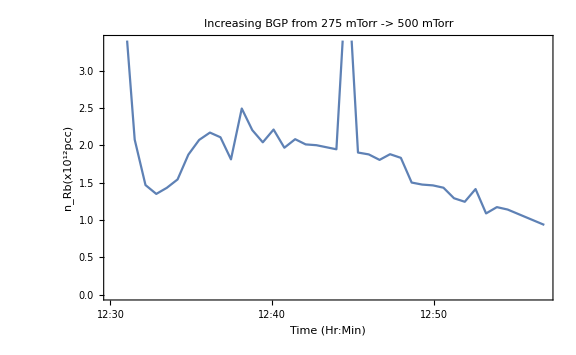

```mathematica
firstFileTimestamp="221152";
numberOfFiles=38;
numDenData=ProcessNumberDensityOverTime[rotationFiles,firstFileTimestamp,baselineAngle,numberOfFiles];
DateListPlot[numDenDataset[All,{"time",#["n_rb"]/1*^12&}],PlotLabel->"Increasing BGP from\n275 mTorr -> 500 mTorr",FrameLabel->{"Time (Hr:Min)","n_Rb(x10^12pcc)"},LabelStyle->18,ImageSize->Large]
```

### Polarization Over Time

```mathematica
numberOfFiles=3;
files=rotationFiles;
baselineAngle=9.82*π/180;

data=ProcessQuickPolarizationOverTime[rotationFiles,"221152",baselineAngle,numberOfFiles,30];
dataset=Dataset[data]
nVsTime=dataset[All,{"time","n"}]
pVsTime=dataset[All,{"time","prbSPlus"}]
temp120To125BGP500=nVsTime;
DateListPlot[Normal[nVsTime]]
```

### Get Baseline Angle From Varying Magnetic Field

Dataset[<>]

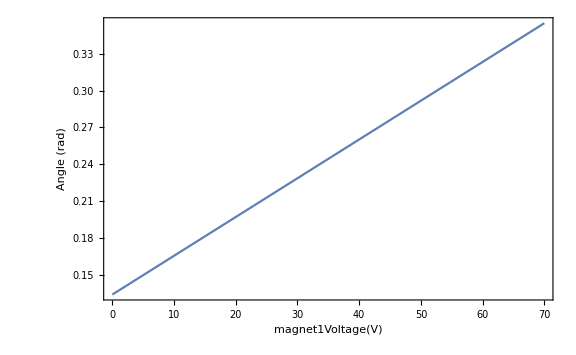

0.134456

θ_o= 0.134456

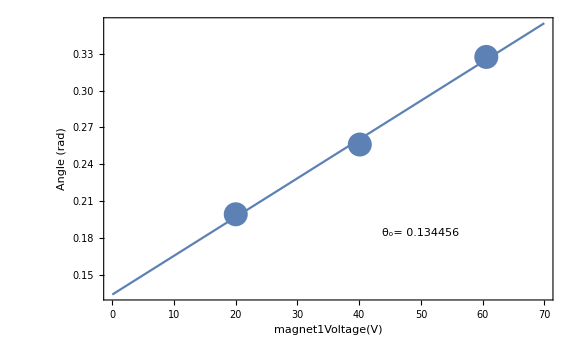

```mathematica
magFieldData=ProcessNumberDensityOverTime[rotationFiles,"121452",baselineAngle,16];
faradayRotationDataset=Dataset[magFieldData][Select[StringContainsQ[#Comments,"no pump"]&]];
yAxis="Angle (rad)";
xAxis="magnet1Voltage(V)";
selectedData=faradayRotationDataset[2;;4,{xAxis,yAxis}]
modelFit=LinearModelFit[Normal[selectedData[All,Values]],x,x];
plotFit=Plot[modelFit[x],{x,0,70},FrameLabel->{xAxis,yAxis}]
modelFit[0]
zeroString="θ_o= "<>ToString[modelFit[0]]
Show[{plotFit,ListPlot[selectedData,FrameLabel->{xAxis,yAxis}],Graphics[Text[zeroString,{50,modelFit[0]+.05}],BaseStyle->15]}]
```

## Initialization Cells

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->24},Frame->True,ImageSize->Large];
SetOptions[ListPlot,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic,Frame->True,PlotStyle->PointSize[.03]];
SetOptions[DateListPlot,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic,Frame->True,PlotStyle->PointSize[.03],LabelStyle->18];
SetOptions[BarChart,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic];

c=2.99792458*^10; (* cm/s *)
re=2.8179*^-13; (* cm *)
cellLength=2.794;(*cm*)
fge=0.34231; (* dimensionless *)
k=4/3; (* dimensionless *)
BdotL; (* G*cm *)
μ=9.2740*^-21; (* g*cm^2*s^-2*G^-1 *)
h=6.6261*^-27; (* cm^2*g/s *)
ν0=377107.463;  (* GHz *)
gHzToHz=1*^9;
nDensC=2*h/(c*re*fge*k*μ)*10^18; (* cm^2*g*s^-1  *  G^-1*cm^-1  *  cm^-1*s  *  cm^-1  *  g^-1*cm^-2*s^2*G  *)
(*Conversion Factor is in 1/(Hz)^2, so we need *10^18 to convert to 1/(GHz)^2*)

colorBlindPallete={RGBColor[230/255,159/255,0],RGBColor[86/255,180/255,233/255],RGBColor[0/255,158/255,115/255],RGBColor[240/255,228/255,66/255],RGBColor[0/255,114/255,178/255],RGBColor[213/255,94/255,0/255],RGBColor[204/255,121/255,167/255],RGBColor[0/255,0/255,0/255]}

SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large];
SetOptions[ListPlot,BaseStyle->{FontSize->24,PointSize[Large]},ImageSize->Large,GridLines->Automatic];
SetOptions[BarChart,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic];

labelSize=14;
color=Red;
low=0;

GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];

(* The coefficients for the polynomial describing the magnetic field of magnet 1 [(c)oefficient of magent (1)]  based on the current.
Assumes x is measured in cm *)
c1x2=.085;
c1x1=-1.907;
c1x0=17.24;
c2x2=0.153;
c2x1=1.866;
c2x0=15.594;

(* The coefficients for the linear relationship between the current and the voltage of the magnets *)
c1v2iSlope=.0504;
c1v2iInt=-.0113;
c2v2iSlope=.0488;
c2v2iInt=-.0069;

(* Calculate the current in each of the magnets based on the voltage *)
i1[voltage_]:=voltage*c1v2iSlope+c1v2iInt;
i2[voltage_]:=voltage*c2v2iSlope+c2v2iInt;

(*Creates a function for obtaining the magnetic field at a given position based on the currents
in the magnets *)
getBEq[i1_,i2_]:=((c1x2 )i1 +(c2x2)i2) x^2 +((c1x1 )i1 +(c2x1)i2) x +((c1x0 )i1 +(c2x0)i2);

CalculateIntegratedMagneticField[voltageMagnet1_,voltageMagnet2_]:=Module[{},
(* Integrates the value of the magnetic field over the length of the cell. *)
Integrate[getBEq[i1[voltageMagnet1],i2[voltageMagnet2]],{x,0,cellLength}](*/100/10000(Divide by 100 to convert to Gauss*meters, Divide by 10000 to convert to Tesla*meters*)
];

(* I love these things. By creating a function with a module you can create "functions" in the traditional C programming sense, where you have multiple inputs with one output. *)
(* ApproximateFrequency calculates the approximate frequency in the missing gap of the frequency measurements that we collected. *)
ApproximateFrequency[data_,columnMissing_,columnReference_,missingEntry_]:=Module[{j,adjacentSpots,referenceSpacing,validEntries,fit}(*These are your local variables that aren't stored beyond the scope of the module.*),
(*Selects the data that is certainly an appropriate measure of wavelength *)
validEntries=Take[data,All,{1,2}];
validEntries=validEntries[Select[#[[columnMissing]]>7000000&]];
(*The "reference column" is the column that is monotonically increasing, we need to know what the size of spaces between these values is *)
referenceSpacing=Abs[data[[2]][[columnReference]]-data[[1]][[columnReference]]];
j=1;
(* This "While" loop accumulates adjacent data points used to approximate the missing frequency, we only want the closest datapoints. *)
While[And[Length[adjacentSpots]<3,Abs[j*referenceSpacing]<1024](* We want a few data points to approximate where our point lies, keep going until we have at least 3*),
adjacentSpots=validEntries[Select[Abs[#[[columnReference]]-missingEntry]≤referenceSpacing*j&]];
j++;
];
fit=LinearModelFit[Normal[adjacentSpots],x,x];
Print[missingEntry];
fit[missingEntry] (* Last line is the "return" statement, all other lines need a semi-colon*)
];

(* This is called on a dataset to fill in all of the missing frequency gaps.*)
FillInMissedFrequencies[dataset_,columnMissing_,columnReference_]:=Module[{referenceSpacing,missingEntries,validEntries,adjacentSpots,estimatedFrequency,linearModel,dataCopy,dataReturn,position,approxValue,data2,k},
dataCopy=dataset;
missingEntries=dataCopy[Select[#columnMissing<7000000&]];
missingEntries=Transpose[Normal[missingEntries]][[columnReference]];
For[k=1,k<=Length[missingEntries],k++,
approxValue=ApproximateFrequency[dataCopy,columnMissing,columnReference,missingEntries[[k]]];
(* Find the index of the missing value in the list *)
position=Position[dataCopy,missingEntries[[k]]][[1,1]];
(* Use the index to insert the approximate value in the data  *)
dataReturn[[position,columnMissing]]=approxValue;
];
dataReturn
];

(* This removes the majority of the data that we're not interested in for Faraday rotation purposes*)
StripFaradayData[data_]:=Drop[Take[data,{rotAnalDataStartRow,-1},{aoutColumn,angleColumn}],None,{wavelengthColumn+1,angleColumn-wavelengthColumn+1}];

(* Converts the wavelength value reported as an integer to a detuning (GHz) *)
ConvertFDayWavelengthToDetune[data_]:=Module[{wavelengthInteger,θ,lists,wavelengthnm,wavelength,detuning},
lists=Transpose[data];
wavelengthInteger=lists[[1]];
θ=lists[[2]];
wavelengthnm=wavelengthInteger/10000;
detuning=c/(wavelengthnm)-ν0;
Transpose[{detuning,θ}]
];

(* Converts the angle of rotation variable reported as a degree to radians.*)
ConvertFDayDegreeToRadian[data_]:=Module[{wavelengthInteger,θ,lists,wavelengthnm,wavelength,detuning,radian},
lists=Transpose[data];
wavelengthInteger=lists[[1]];
θ=lists[[2]];
radian=θ*Pi/180;
Transpose[{wavelengthInteger,radian}]
];

SubtractLinearSlope[data_,linearSlope_]:=Module[{detuning,angle,dataTranspose},
dataTranspose=Transpose[data];
detuning=dataTranspose[[1]];
angle=dataTranspose[[2]];
angle=angle-linearSlope*detuning;
Transpose[{detuning,angle}]
];
ZeroDataWithAsymptote[data_,nearResonanceCut_,largeDetuningCut_]:=Module[{model, dataset,nlmFit,replacements,temp,a1x,a2x,bx,θ0x,δx},
dataset=Dataset[data];
dataset=dataset[Select[Abs[#[[1]]]<largeDetuningCut&]];
dataset=dataset[Select[Abs[#[[1]]]>nearResonanceCut&]];

model=a1x/(δx)^2+a2x/(δx)^4+θ0x;
nlmFit =NonlinearModelFit[Normal[dataset],model,{{a1x,1},{a2x,1},{θ0x,0}},δx];
replacements=nlmFit["BestFitParameters"];

dataset =Transpose[Normal[data]];
dataset[[2]]=dataset[[2]]-θ0x/.replacements;
Transpose[{dataset[[1]],dataset[[2]]}]
];

GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"-> "",":"->""}]->joinedWithSpaces];
,
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"->"",":"->""}]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
SetAttributes[GetFileDataset,Listable];
SetAttributes[GetFileHeaderInfo,Listable];
SetAttributes[ImportFile,Listable];

ProcessFaradayScanFileFromFileName[fileName_,baselineAngle_]:=Module[{i,index,file,header, datasetRaw,datasetZeroLineRemoved,dataset,detAndAngle,a1,a2,maxmin,nlmFit,replacements,δ,θ0,plot,errors,fitRangeMin,fitRangeMax,n,nErr,finalResult,modelA4,modelA2,model,startPoints,modelString,results,n1pt,det,angle},
file=ImportFile[fileName];
header=file[[1]];
datasetRaw=file[[2]];
datasetZeroLineRemoved=datasetRaw[Select[#Wavelength≠0&]];
dataset=datasetZeroLineRemoved[All,<|#,"DETUNING"->c/100/(#Wavelength/10000)-ν0|>&] ;(* c is in cm/s*)
detAndAngle=dataset[All,<|"DET"->#DETUNING,"ANG"->#angle*π/180|>&];

$Assumptions=a1>0;
$Assumptions=a2>0;
cutoffs={6,40};
dataset=Normal[detAndAngle[Select[Abs[#DET]>cutoffs[[1]]&]][[All,Values]]];
det=Transpose[dataset][[1]];
angle=Transpose[dataset][[2]];
(* Takes the Maximum and minimum from the 2nd column of the dataset*)
maxmin={dataset[Max,2],dataset[Min,2]};

i=1;
modelA4=a1/(δ)^2+a2/(δ)^4+θ0;
modelString="A_1/(δ)^2+A_2/(δ)^4+θ_o";
modelA2=a1/(δ)^2+θ0;
(*
model={modelA4,a1>0,a2>0};
startPoints={{a1,1},{a2,1},{θ0,0}};
*)
model={modelA2,a1>0};
startPoints={{a1,1},{θ0,0}};

nlmFit =NonlinearModelFit[Normal[dataset],model,startPoints,δ];
replacements=nlmFit["BestFitParameters"];
fitRangeMin=-30;
fitRangeMax=30;
plot=Plot[Legended[Evaluate[model(*/.(θ0->baselineAngle)*)/.replacements],modelString],{δ,fitRangeMin,fitRangeMax},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->colorBlindPallete[[i]],LabelStyle->labelSize];
errors=nlmFit["ParameterErrors"];

n=(a1/.replacements)* nDensC/CalculateIntegratedMagneticField[header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];
n1pt=NumberDensityFromOneMeasurement[angle[[-1]],baselineAngle,det[[-1]],header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];
errors=nlmFit["ParameterErrors"];
nErr=errors[[1]]*nDensC/CalculateIntegratedMagneticField[header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];

finalResult=Show[plot,ListPlot[Legended[Normal[dataset],"Data Points"],LabelStyle->labelSize,PlotStyle->colorBlindPallete[[-1]],BaseStyle->{FontSize->24,PointSize[Large]},ImageSize->Large,GridLines->Automatic],Epilog->Inset[Style[n,14],{20,.025}],AxesLabel->{"Detuning\n(GHz)","Plane of Polarization (rad)"},ImageSize->Large,PlotRange->All];

results=<|"n_rb"->n/1*^12,"n_rberr"->nErr/1*^12,"n1pt"->n1pt/1*^12,"measuredTheta_0"-> baselineAngle,"calcTheta_0"->θ0/.replacements,"plot"-> finalResult,"dataset"->dataset,"time"->ExtractTimeInfoFromFileNameString[header["File"]]|>;
AppendTo[results,header]

];

ProcessFaradayScanFile[scanFiles_,fileTimestamp_,baselineAngle_]:=Module[{i,index,file,header, datasetRaw,datasetZeroLineRemoved,dataset,detAndAngle,a1,a2,maxmin,nlmFit,replacements,δ,θ0,plot,errors,fitRangeMin,fitRangeMax,n,nErr,finalResult,modelA4,modelA2,model,startPoints,modelString,results},
index=GetIndexOfFilenameFromTimestamp[scanFiles,fileTimestamp];
ProcessFaradayScanFileFromFileName[scanFiles[[index]],baselineAngle]
];

PolarizationFromOneMeasurement[angleShift_,detuning_,numberDensity_]:=
(-4*(detuning*gHzToHz)*angleShift)/(re*c*fge*cellLength*numberDensity);

NumberDensityFromOneMeasurement[rotatedAngle_,baselineAngle_,detuning_,voltage1_,voltage2_]:=
(* Angle should be input in radians *)
((rotatedAngle-baselineAngle)*2*h*(detuning*gHzToHz)^2)/(μ*re*fge*c*k*CalculateIntegratedMagneticField[voltage1,voltage2]);

(* The current dataset I am processing doesn't have the detuning value in the header, so I am going to pass it in. In the future, it should be recorded in the header, so the detuning argument won't be used. By default it will go to -300, which means that the program should look for its value within the datafile.*)
NumberDensityFromFaradayRotation[fileName_,baselineAngle_,detuning_:-300]:=Module[{file,header,rawDataset,rotatedAngle,wavelength,results,det},
file=ImportFile[fileName];
header=file[[1]];
rawDataset=file[[2]];
rotatedAngle=Normal[rawDataset][[1]]["angle"]*π/180;
wavelength=header["Wavelength"];
If[detuning==-300,det=c/100/(wavelength/10000)-ν0;,det=detuning];
n=NumberDensityFromOneMeasurement[rotatedAngle,baselineAngle,det,header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];
results=<|"n_Rb(pcc x 10^12)"->n/1*^12,"Angle (rad)"-> rotatedAngle|>;
AppendTo[results,<|"time"->ExtractTimeInfoFromFileNameString[header["File"]]|>];
AppendTo[results,header]
];

ProcessNumberDensityOverTime[scanFiles_,fileTimestamp_,baselineAngle_,numberOfRotationFiles_]:=Module[{index,result,resultsList,i},
resultsList={};
index=GetIndexOfFilenameFromTimestamp[scanFiles,fileTimestamp];
For[i=1,i<=numberOfRotationFiles,i++,
result=NumberDensityFromFaradayRotation[scanFiles[[index+(i-1)]],baselineAngle];
AppendTo[resultsList,result];
];
resultsList
];

ProcessQuickPolarizationOverTime[scanFiles_,fileTimestamp_,baselineAngle_,numberOfFiles_,numberOfQuickScans_]:=Module[{index,result,resultsList,i},
resultsList={};
index=GetIndexOfFilenameFromTimestamp[scanFiles,fileTimestamp];
For[i=1,i<=numberOfQuickScans,i++,
result=ProcessQuickPolarizationFileSequence[scanFiles,(index+(i-1)*numberOfFiles),baselineAngle,numberOfFiles];
AppendTo[resultsList,result];
];
resultsList
];

ProcessQuickPolarizationFileSequence[scanFiles_,fileIndex_,baselineAngle_,numberOfFiles_]:=Module[{files,index,headers,rawDatasets,datasetsCleaned,datasets,detAndAngles,fileNames,wavelength,none,sPlus,sMinus,detunings,n,prbAvg,prbSPlus,prbSMinus,results},

files=scanFiles;
index=fileIndex;
If[numberOfFiles==4,
fileNames=<|"no"->files[[index]],"pi"->files[[index+1]],"s+"->files[[index+2]],"s-"->files[[index+3]]|>;,
If[numberOfFiles==3,
fileNames=<|"no"->files[[index]],"s+"->files[[index+1]],"s-"->files[[index+2]]|>;,
If[numberOfFiles==2,
fileNames=<|"no"->files[[index]],"s+"->files[[index+1]]|>;
]
]
];

files=<||>;
headers=<||>;
rawDatasets=<||>;
datasetsCleaned=<||>;
datasets=<||>;
detAndAngles=<||>;

For[i=1,i≤Length[fileNames],i++,
AppendTo[files,Keys[fileNames][[i]]->ImportFile[fileNames[[i]]]];
AppendTo[headers,Keys[files][[i]]->files[[i]][[1]]];
AppendTo[rawDatasets,Keys[files][[i]]->files[[i]][[2]]];
wavelength=headers[[i]]["Wavelength"];
AppendTo[datasets,Keys[files][[i]]->rawDatasets[[i]][All,<|#,"DETUNING"->c/100/(wavelength/10000)-ν0|>&] ];(* c is in cm/s*)
AppendTo[detAndAngles,Keys[files][[i]]->Normal[datasets[[i]][All,<|"DET"->#DETUNING,"ANG"->#angle*π/180|>&][All,Values]]];
];

none=Transpose[detAndAngles["no"]][[2]];
sPlus=Transpose[detAndAngles["s+"]][[2]];
(*Correct for wrapping *)
sMinus=Transpose[detAndAngles["s-"]][[2]];
detunings=Transpose[detAndAngles["s+"]][[1]];

n=NumberDensityFromOneMeasurement[none[[1]],baselineAngle,detunings[[1]],headers["no"]["magnet1Voltage(V)"],headers["no"]["magnet2Voltage(V)"]];
prbAvg=PolarizationFromOneMeasurement[(sPlus-sMinus)[[1]]/2,detunings[[1]],n];
prbSPlus=PolarizationFromOneMeasurement[(sPlus-none)[[1]],detunings[[1]],n];
prbSMinus=PolarizationFromOneMeasurement[(sMinus-none)[[1]],detunings[[1]],n];

results=<|"n"-> n, "prbAvg"->prbAvg,"prbSPlus"->prbSPlus,"prbSMinus"->prbSMinus|>;
AppendTo[results,<|"time"->ExtractTimeInfoFromFileNameString[headers["no"]["File"]]|>];
AppendTo[results,headers["no"]]
];

ProcessRbPolarizationFileSequence[scanFiles_,fileTimestamp_,baselineAngle_,numberOfFiles_]:=Module[{i,index,noPumpFile,piPumpFile,sPlusPumpFile,sMinusPumpFile,header, datasetRaw,datasetZeroLineRemoved,dataset,detAndAngle,a1,a2,maxmin,nlmFit,replacements,δ,θ0,plot,errors,fitRangeMin,fitRangeMax,n,nErr,finalResult,modelA4,modelA2,model,startPoints,modelString,Cpar,frequencyCutoff,files,headers,rawDatasets,datasetsCleaned,datasets,detAndAngles,fileNames,none,sPlus,sMinus,polDataBoth,detunings,x,lm,polPlot,dataLine,slope,pol,σSlope,σDensity,σp,results,polDataSPlus,polDataSMinus,polData,polDataLabels,stringHead,j},

frequencyCutoff={0,40};


Cpar=(4*gHzToHz)/(re*c*fge*cellLength);
index=GetIndexOfFilenameFromTimestamp[scanFiles,fileTimestamp];
If[numberOfFiles==4,
fileNames=<|"no"->scanFiles[[index]],"pi"->scanFiles[[index+1]],"s+"->scanFiles[[index+2]],"s-"->scanFiles[[index+3]]|>;,
If[numberOfFiles==3,
fileNames=<|"no"->scanFiles[[index]],"s+"->scanFiles[[index+1]],"s-"->scanFiles[[index+2]]|>;,
If[numberOfFiles==2,
fileNames=<|"no"->scanFiles[[index]],"s+"->scanFiles[[index+1]]|>;
]
]
];

files=<||>;
headers=<||>;
rawDatasets=<||>;
datasetsCleaned=<||>;
datasets=<||>;
detAndAngles=<||>;

For[i=1,i≤Length[fileNames],i++,
AppendTo[files,Keys[fileNames][[i]]->ImportFile[fileNames[[i]]]];
AppendTo[headers,Keys[files][[i]]->files[[i]][[1]]];
AppendTo[rawDatasets,Keys[files][[i]]->files[[i]][[2]]];
AppendTo[datasetsCleaned,Keys[files][[i]]->rawDatasets[[i]][Select[#Wavelength≠0&]]];
AppendTo[datasets,Keys[files][[i]]->datasetsCleaned[[i]][All,<|#,"DETUNING"->c/100/(#Wavelength/10000)-ν0|>&][Select[Abs[#DETUNING]>frequencyCutoff[[1]]&]] ];(* c is in cm/s*)
AppendTo[detAndAngles,Keys[files][[i]]->Normal[datasets[[i]][All,<|"DET"->#DETUNING,"ANG"->#angle*π/180|>&][All,Values]]];
];

$Assumptions=a1>0;
$Assumptions=a2>0;

none=Transpose[detAndAngles["no"]][[2]];
sPlus=Transpose[detAndAngles["s+"]][[2]];
For[j=1,j≤Length[sPlus],j++,
If[sPlus[[j]]<0,sPlus[[j]]=sPlus[[j]]+π];
];
detunings=Transpose[detAndAngles["s+"]][[1]];

If[numberOfFiles==2,
polDataBoth=Transpose[{1/detunings,(sPlus-none)}];
polData={polDataBoth};
polDataLabels={""};
,
sMinus=Transpose[detAndAngles["s-"]][[2]];
polDataBoth=Transpose[{1/detunings,(sPlus-sMinus)/2}];
polDataSPlus=Transpose[{1/detunings,(sPlus-none)}];
polDataSMinus=Transpose[{1/detunings,(sMinus-none)}];
polData={polDataBoth,polDataSPlus,polDataSMinus};
polDataLabels={"","s+","s-"};
];
results=<||>;
For[j=1,j≤Length[polData],j++,
lm=LinearModelFit[polData[[j]],x,x];
polPlot=Plot[lm[x],{x,0,1/Max[detunings]}];

slope=lm["BestFitParameters"][[2]];


dataLine=ProcessFaradayScanFileFromFileName[fileNames["no"],baselineAngle];

n=dataLine["n_rb"]*1*^12;
pol=-Cpar*slope/n;
σSlope=lm["ParameterErrors"][[2]];
σDensity=dataLine["n_rberr"]*1*^12;
σp=Sqrt[pol^2*((σSlope/slope)^2+(σDensity/n)^2)];
plot=Show[{ListPlot[polData[[j]]],polPlot},AxesOrigin-> {0,0},PlotRange->{Automatic,Automatic},AxesLabel->{"1/Detuning\n(GHz^-1)","(θ_(S+))/2"},LabelStyle->labelSize,ImageSize->Large];
stringHead="p_rb";
AppendTo[results,<|StringJoin[stringHead,polDataLabels[[j]]]->pol,StringJoin[stringHead,polDataLabels[[j]],"err"]->σp,StringJoin[stringHead,polDataLabels[[j]],"errSlope"]->σSlope/slope,StringJoin[stringHead,polDataLabels[[j]],"errDens"]->σDensity/n,StringJoin[stringHead,polDataLabels[[j]],"Slope"]->slope,StringJoin[stringHead,polDataLabels[[j]],"Slopeerr"]->σSlope,StringJoin[stringHead,polDataLabels[[j]],"plot"]->plot|>
];
];

AppendTo[results,<|"n_rb"->n/1*^12,"n_rberr"->σDensity/1*^12|>];
AppendTo[results,<|"time"->ExtractTimeInfoFromFileNameString[headers["no"]["File"]]|>];
AppendTo[results,headers["no"]]
];

ExtractTimeInfoFromFileNameString[fileNameString_]:=Module[{lastChars,date,year,month,day,hour,min,sec,do},
lastChars=StringTake[fileNameString,-21];
date=StringTake[lastChars,17];
year=StringTake[date,{1,4}];
month=StringTake[date,{6,7}];
day=StringTake[date,{9,10}];
hour=StringTake[date,{12,13}];
min=StringTake[date,{14,15}];
sec=StringTake[date,{16,17}];
do=DateObject[{Interpreter["Number"][year],Interpreter["Number"][month],Interpreter["Number"][day],Interpreter["Number"][hour],Interpreter["Number"][min],Interpreter["Number"][sec]}]
];
```

{RGBColor[Rational[46, 51], Rational[53, 85], 0],RGBColor[Rational[86, 255], Rational[12, 17], Rational[233, 255]],RGBColor[0, Rational[158, 255], Rational[23, 51]],RGBColor[Rational[16, 17], Rational[76, 85], Rational[22, 85]],RGBColor[0, Rational[38, 85], Rational[178, 255]],RGBColor[Rational[71, 85], Rational[94, 255], 0],RGBColor[Rational[4, 5], Rational[121, 255], Rational[167, 255]],RGBColor[0, 0, 0]}

```mathematica
det=c/100/794.9880-ν0;
NumberDensityFromOneMeasurement[13.66,.125*180/π,det,63.2,65.2]
```

1.53098×10^14

```mathematica
timeString="113500";
index=GetIndexOfFilenameFromTimestamp[scanFiles,timeString];
fileName=scanFiles[[index]];
dataset=ImportFile[fileName][[2]];

columnMissing="Wavelength";
referenceColumn="Aout";
(*Finds the values of AOUT that we need to calculate *)
invalidEntries=Normal[dataset[Select[#[columnMissing]<7000000&]][All,{referenceColumn}][[All,Values]]][[1]];

(*Selects the data that is certainly an appropriate measure of wavelength *)
validEntries=dataset[Select[#[columnMissing]>7000000&]];
(*Removes everything from the dataset but the two relevant columns *)
datasetForFit=Normal[validEntries[[All,{referenceColumn,columnMissing}]][[All,Values]]];
(*Makes a linear model from those two columns.*)
lmFit=LinearModelFit[datasetForFit,x,x]

N[lmFit[580],8]

justNumbers=Normal[datasetForFix];
pos=Position[justNumbers,invalidEntries[[1]]][[1]]
justNumbers[[pos[[1]],2]]=N[lmFit[justNumbers[[pos[[1]],pos[[2]]]]],7];
blerf=Normal[dataset];
Join[justNumbers,blerf];
newDataset=dataset[All,<|justNumbers|>&]
```

FittedModel[7.94951×10^6+0.600935 x]

7.94986×10^6

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

Dataset[<>]

```mathematica
(*The "reference column" is the column that is monotonically increasing, we need to know what the size of spaces between these values is *)
referenceSpacing=Abs[data[[2]][[columnReference]]-data[[1]][[columnReference]]];
j=1;
(* This "While" loop accumulates adjacent data points used to approximate the missing frequency, we only want the closest datapoints. *)
While[And[Length[adjacentSpots]<3,Abs[j*referenceSpacing]<1024](* We want a few data points to approximate where our point lies, keep going until we have at least 3*),
adjacentSpots=validEntries[Select[Abs[#[[columnReference]]-missingEntry]≤referenceSpacing*j&]];
j++;
];
fit=LinearModelFit[Normal[adjacentSpots],x,x];
Print[missingEntry];
fit[missingEntry] (* Last line is the "return" statement, all other lines need a semi-colon*)
];
```